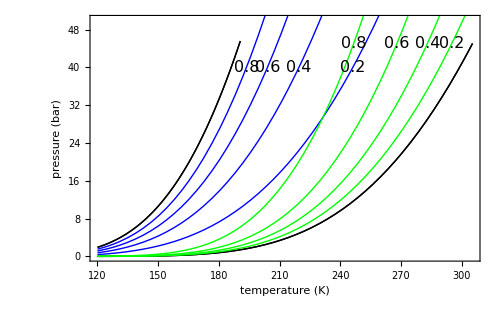

```mathematica
Module[{T0,Tc1,Tc2,Psat1,Psat2,Px,Py},
T0=120;

Tc1=190.6;
Tc2=305.4;

Psat1[T_]:=10^(3.989-443/(T-0.49));
Psat2[T_]:=10^(3.94-660/(T-16.7));

Px[x_,T_]:=x*Psat1[T]+(1-x)*Psat2[T];
Py[x_,T_]:=(x/Psat1[T]+(1-x)/Psat2[T])^-1;

Show[
Plot[{Px[1,T],Py[1,T]},{T,T0,Tc1},PlotStyle->{{Thick,Black}}],
Plot[{Px[0,T],Py[0,T]},{T,T0,Tc2},PlotStyle->{{Thick,Black}}],
Table[Plot[Px[x,T],{T,T0,Tc2},PlotStyle->{Thick,Blue}],{x,0.2,0.8,0.2}],
Table[Plot[Py[x,T],{T,T0,Tc2},PlotStyle->{Thick,Green}],{x,0.2,0.8,0.2}],
Graphics[{
Table[Text[Style[x,16,Background->White],{t/.Quiet@FindRoot[Px[x,t]==40,{t,T0}],40}],{x,0.2,0.8,0.2}],
Table[Text[Style[x,16,Background->White],{t/.Quiet@FindRoot[Py[x,t]==45,{t,T0}],45}],{x,0.2,0.8,0.2}]
}],
Axes->False,
Frame->True,
FrameLabel->{Style["temperature (K)",17],Style["pressure (bar)",17]},
LabelStyle->{Black,14},
ImageSize->500,
PlotRange->{0,50}
]
]
```